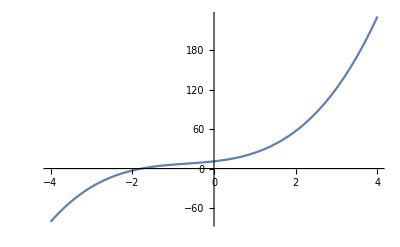

```mathematica
y[x_]:=2x^3+4x^2+7x+11
Plot[y[x],{x,-4,4}]
```

```mathematica
z[x_]:=2x^3+-6.09x^2+7x+152.27
z[0]
z[1]
z[2]
z[3]
z[4]
z[-1]
z[-2]
z[-3]
z[-4]
z[5]
z[-5]
z[6]
z[-6]
z[20]
z[-25]
z[-3]
```

152.27

155.18

157.91

172.46

210.83

137.18

97.91

22.46

-101.17

285.02

-284.98

407.03

-540.97

13856.3

-35079.

22.46

```mathematica
D[{(p- a*x^3-b*x^2-c*x-d)^2}, a]
D[{(p- a*x^3-b*x^2-c*x-d)^2}, b]
D[{(p- a*x^3-b*x^2-c*x-d)^2}, c]
D[{(p- a*x^3-b*x^2-c*x-d)^2}, d]
```

{-2 x^3 (-d+p-c x-b x^2-a x^3)}

{-2 x^2 (-d+p-c x-b x^2-a x^3)}

{-2 x (-d+p-c x-b x^2-a x^3)}

{-2 (-d+p-c x-b x^2-a x^3)}

```mathematica
s=∑_(i=0)^n {(p[i]- a*x[i]^3-b*x[i]^2-c*x[i]-d)^2}
D[{s}, a]
D[{s}, b]
D[{s}, c]
D[{s}, d]
```

{∑_(i=0)^n (-d+p[i]-c x[i]-b x[i]^2-a x[i]^3)^2}

{{∑_(i=0)^n (2 d x[i]^3-2 p[i] x[i]^3+2 c x[i]^4+2 b x[i]^5+2 a x[i]^6)}}

{{∑_(i=0)^n (2 d x[i]^2-2 p[i] x[i]^2+2 c x[i]^3+2 b x[i]^4+2 a x[i]^5)}}

{{∑_(i=0)^n (2 d x[i]-2 p[i] x[i]+2 c x[i]^2+2 b x[i]^3+2 a x[i]^4)}}

{{∑_(i=0)^n (2 d-2 p[i]+2 c x[i]+2 b x[i]^2+2 a x[i]^3)}}